```mathematica
init=(x-1.5)^2+y^2≤0.25//Rationalize;
unsafe=(x+1)^2+(y+1)^2≤0.16//Rationalize;
Q=-3≤x≤3 && -3≤y≤3; (* bounded evolution constraint *)
vf=-{-2(y+1)^2,-(x+1)}//Rationalize
vars={x,y};
```

{2 (1+y)^2,1+x}

```mathematica
problem={init, {vf,vars,Q}, Not[unsafe]} (* Safety verification problem *)
```

{(-3/2+x)^2+y^2≤1/4,{{2 (1+y)^2,1+x},{x,y},-3≤x≤3&&-3≤y≤3},(1+x)^2+(1+y)^2>4/25}

```mathematica
(* Exponential-type barrier generation. Arguments: [max degree, lambda (in B' ≤ lambda*B ), safety problem *)
BC=BarrierCertificate`LPBarrier[5,1,problem]
```

458022696816440971909216775/124191727248293694464369926784-(101396665435319518973940325 x)/15523965906036711808046240848-(5437060798591567265861775 x^2)/62095863624146847232184963392-(2665471401119510789217875 x^3)/46571897718110135424138722544-(53503099222036262388125 x^4)/124191727248293694464369926784-(9493948827337263880625 x^5)/93143795436220270848277445088-(603823357573317466060535775 y)/124191727248293694464369926784-(43406423609241413583953825 x y)/31047931812073423616092481696-(498011051261139202034875 x^2 y)/62095863624146847232184963392-(710874935936814005028125 x^3 y)/46571897718110135424138722544-(25878839854478678109375 x^4 y)/124191727248293694464369926784-(1914817020865600546320075 y^2)/7761982953018355904023120424-(12147771182870019761922375 x y^2)/31047931812073423616092481696+(117003906599402019269375 x^2 y^2)/31047931812073423616092481696-(29363049739370672939375 x^3 y^2)/23285948859055067712069361272-(961165509371310029548275 y^3)/31047931812073423616092481696-(713156807451896631066375 x y^3)/31047931812073423616092481696-(149430786026890829375 x^2 y^3)/15523965906036711808046240848-(13890078517346651362125 y^4)/970247869127294488002890053-(4630026172448883787375 y^5)/970247869127294488002890053

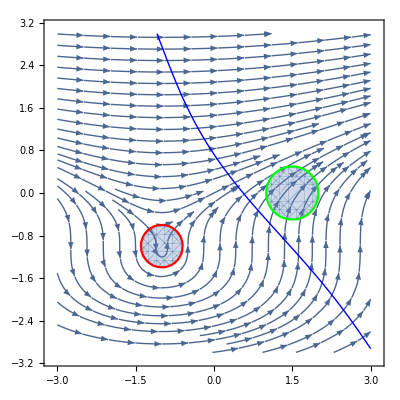

```mathematica
Show[
StreamPlot[vf,{x,-3,3},{y,-3,3}],
RegionPlot[init, {x,-3,3},{y,-3,3}, BoundaryStyle->Green],
RegionPlot[unsafe, {x,-3,3},{y,-3,3}, BoundaryStyle->Red],
ContourPlot[BC==0, {x,-3,3},{y,-3,3}, ContourStyle->Directive[Thick, Blue]]
]
```

```mathematica
(* SMTLIB converter code *)
SMTLIB[a_Times]:="(* "<>StringRiffle[SMTLIB/@List@@a]<>")"
SMTLIB[a_Plus]:="(+ "<>StringRiffle[SMTLIB/@List@@a]<>")"
SMTLIB[a_Power]:="(* "<>StringRiffle[SMTLIB/@Table[(List@@a)[[1]],(List@@a)[[2]]]]<>")"
SMTLIB[a_Rational]:="(/ "<>StringRiffle[SMTLIB/@{Numerator[a],Denominator[a]}]<>")"
SMTLIB[a_Equal]:="(assert (= "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_GreaterEqual]:="(assert (>= "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_LessEqual]:="(assert (<= "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_Less]:="(assert (< "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_Greater]:="(assert (> "<>StringRiffle[SMTLIB/@List@@a]<>"))"
SMTLIB[a_List]:=StringRiffle[SMTLIB/@a, "\n"]
SMTLIB[a_]:=StringReplace[ToString[a],"λ"->"LAMBDA"]

SMTLIBvars[vars_List]:=StringRiffle[Map["(declare-fun "<>StringReplace[ToString[#],"λ"->"LAMBDA"]<>" () Real)"&, vars], "\n"]
SMTLIBlogic[logic_String]:="(set-logic "<>logic<>")"
SMTLIBgetvalue[vars_List]:="(get-value ("<>StringRiffle[SMTLIB/@vars]<>"))"
```

```mathematica
(* Uncomment the Throw in BC implementation to use this and re-run BC *)
(* 
lpvars=(Variables/@(First/@BC))//Flatten//DeleteDuplicates//Sort;
"(set-option:print-success true)"<>"\n"<>
"(set-option:produce-models true)"<>"\n"<>
SMTLIBlogic["QF_LRA"]<>"\n"<>
SMTLIBvars[lpvars]<>"\n"<>
SMTLIB[ BC]<>"\n"<>
"(check-sat)"<>"\n"<>
SMTLIBgetvalue[lpvars]<>"\n"<>
"(get-model)"<>"\n"<>
"(exit)"
*)
```

```mathematica
(* MATLAB BC generation - Make sure MatLink is installed correctly *)
BCM=BarrierCertificate`LPBarrierMATLAB[5,1,problem]
```

{0.-0.00654123 x-0.000018547 x^2-0.0000334775 x^3-1.09507×10^-6 x^4-6.28796×10^-8 x^5-0.0119267 y-0.00153627 x y-0.000238131 x^2 y-4.70081×10^-6 x^3 y-3.98145×10^-7 x^4 y-0.002718 y^2-0.000469337 x y^2-6.79474×10^-6 x^2 y^2-0.00145226 y^3-0.0000300382 x y^3-4.52983×10^-6 x^2 y^3-0.000114286 y^4-1.10359×10^-6 x y^4-0.0000461558 y^5}

```mathematica
(* truncating numeric coefficients *)
PolyClean[P_, vrs_List, thresh_]:=FromCoefficientRules[Map[#/.{Rule[a_,b_]:>Rule[a,If[Abs[b]≤thresh, 0, b]]} &,CoefficientRules[P,vrs]],vrs]
```

```mathematica
BCMclean=PolyClean[BCM[[1]],vars, 1/100000]
```

-0.00654123 x-0.000018547 x^2-0.0000334775 x^3-0.0119267 y-0.00153627 x y-0.000238131 x^2 y-0.002718 y^2-0.000469337 x y^2-0.00145226 y^3-0.0000300382 x y^3-0.000114286 y^4-0.0000461558 y^5

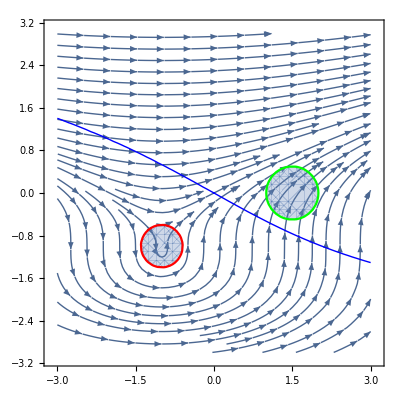

```mathematica
Show[
StreamPlot[vf,{x,-3,3},{y,-3,3}],
RegionPlot[init, {x,-3,3},{y,-3,3}, BoundaryStyle->Green],
RegionPlot[unsafe, {x,-3,3},{y,-3,3}, BoundaryStyle->Red],
ContourPlot[BCMclean==0, {x,-3,3},{y,-3,3}, ContourStyle->Directive[Thick, Blue]]
]
```